#### Week 8: Hw #7

#### Problem #9)

```mathematica
Integrate[I*Pi*DiracDelta[x-1](1/(2*(x-1))),{x,0,∞}]
```

Integrate::idiv: Integral of (ⅈ π DiracDelta[-1+x])/(2 (-1+x)) does not converge on {0,∞}.

∫_0^∞ (ⅈ π DiracDelta[-1+x])/(2 (-1+x))ⅆx

```mathematica
Integrate[I*Pi*DiracDelta[x-1](-1/(2*(x+1))),{x,0,∞}]
```

-(ⅈ π)/4

```mathematica
Integrate[1/(2Pi I)*(1/(x-1))*(-1/(2(x+1))),{x,0,∞},PrincipalValue->True]
```

0

```mathematica
Integrate[1/(2Pi I)*(1/(x-1))*(1/(2(x-1))),{x,0,∞},PrincipalValue->True]
```

Integrate::idiv: Integral of -ⅈ/(4 π (-1+x)^2) does not converge on {0,∞}.

Integrate[-ⅈ/(4 π (-1+x)^2),{x,0,∞},PrincipalValue→True]

```mathematica
Integrate[1/(x-1)^2,{x,0,∞},PrincipalValue->True]
```

Integrate::idiv: Integral of 1/(-1+x)^2 does not converge on {0,∞}.

Integrate[1/(-1+x)^2,{x,0,∞},PrincipalValue→True]

#### Problem #10)

adiabatic approximation

```mathematica
chi[λ_]:=1/(w^2-1-λ)
```

λ = 1/4

```mathematica
1/Sqrt[5.]
```

0.447214

```mathematica
Solve[chi[1/2]^-1==0,w]
```

{{w→-√(3/2)},{w→√(3/2)}}

```mathematica
0.5*Sqrt[2/3]
```

0.408248

```mathematica
1/(2Sqrt[2.])
```

0.353553

Exact

```mathematica
Solve[x^4-21/8 x^2+185/64==0,x]//N
```

{{x→-1.22733+0.440275 ⅈ},{x→1.22733-0.440275 ⅈ},{x→-1.22733-0.440275 ⅈ},{x→1.22733+0.440275 ⅈ}}

```mathematica
(x^2-1-λ-(λ^2 x^2)/(x^2-2-λ-λ^2))^-1//Together
```

(-2+x^2-λ-λ^2)/(2-3 x^2+x^4+3 λ-2 x^2 λ+2 λ^2-2 x^2 λ^2+λ^3)

```mathematica
χ[λ_]:=(-2+x^2-λ-λ^2)/(2-3 x^2+x^4+3 λ-2 x^2 λ+2 λ^2-2 x^2 λ^2+λ^3)
χ[0.5]
```

(-2.75+x^2)/(4.125-4.5 x^2+x^4)

```mathematica
Solve[4.125-4.5 x^2+x^4==0,x]
```

{{x→-1.79395},{x→-1.13215},{x→1.13215},{x→1.79395}}

```mathematica
(x^2-2.75)/((x+1.1322)(x+1.7940)(x-1.7940))/.x->1.1322
```

0.334795

```mathematica
(x^2-2.75)/((x+1.1322)(x+1.7940)(x-1.1322))/.x->1.7940
```

0.0674166

```mathematica
χ[0.25]
```

(-2.3125+x^2)/(2.89063-3.625 x^2+x^4)

```mathematica
Solve[2.890625-3.625 x^2+x^4==0,x]
```

{{x→-1.56225},{x→-1.08829},{x→1.08829},{x→1.56225}}

```mathematica
(x^2-2.3125)/((x+1.08829)(x+1.5623)(x-1.5623))/.x->1.08824
```

0.412541

```mathematica
(x^2-2.3125)/((x+1.08829)(x+1.5623)(x-1.08829))/.x->1.5623
```

0.0326767

```mathematica
χ[1]
```

(-4+x^2)/(8-7 x^2+x^4)

```mathematica
Solve[8-7. x^2+x^4==0,x]
```

{{x→-2.35829},{x→-1.19935},{x→1.19935},{x→2.35829}}

```mathematica
(x^2-4)/((x+1.19935)(x+2.3583)(x-2.3583))/.x->1.1994
```

0.258991

```mathematica
(x^2-4)/((x+1.19935)(x+2.3583)(x-1.19935))/.x->2.35829
```

0.0802971

```mathematica
χ[λ]
```

(-2+x^2-λ-λ^2)/(2-3 x^2+x^4+3 λ-2 x^2 λ+2 λ^2-2 x^2 λ^2+λ^3)

```mathematica
Solve[2-3 x^2+x^4+3 λ-2 x^2 λ+2 λ^2-2 x^2 λ^2+λ^3==0,x]//FullSimplify
```

{{x→-√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2)))},{x→√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2)))},{x→-(√(3+2 λ (1+λ)+√(1+4 λ^2 (2+λ+λ^2))))/(√2)},{x→√(λ+λ^2+1/2 (3+√(1+4 λ^2 (2+λ+λ^2))))}}

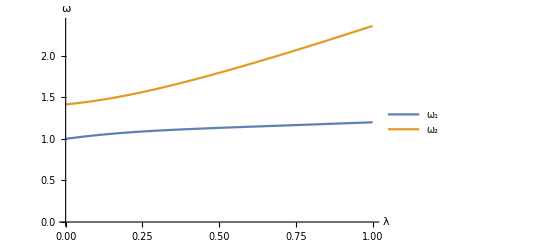

```mathematica
Plot[{√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2))),√(λ+λ^2+1/2 (3+√(1+4 λ^2 (2+λ+λ^2))))},{λ,0,1},AxesLabel->{"λ","ω"},PlotLegends->{"ω_1","ω_2"},PlotRange->{0,2.4}]
```

```mathematica
oscil[λ_]:=(-2+x^2-λ-λ^2)/((x+√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2))))(x-√(λ+λ^2+1/2 (3+√(1+4 λ^2 (2+λ+λ^2)))))(x+(√(3+2 λ (1+λ)+√(1+4 λ^2 (2+λ+λ^2))))/(√2)))/.x->√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2)))
```

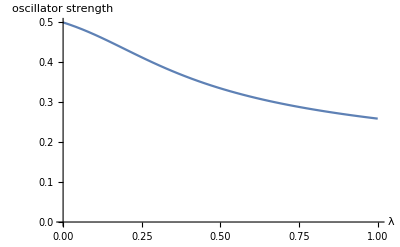

```mathematica
Plot[oscil[y]//N,{y,0,1},PlotRange->{0,0.5},AxesLabel->{"λ","oscillator strength"}]
```

Error plot between adiabatic approximation and exact

```mathematica
Solve[w^2-1-λ==0,w]
```

{{w→-√(1+λ)},{w→√(1+λ)}}

```mathematica
Solve[2-3 x^2+x^4+3 λ-2 x^2 λ+2 λ^2-2 x^2 λ^2+λ^3==0,x]//FullSimplify
```

{{x→-√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2)))},{x→√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2)))},{x→-(√(3+2 λ (1+λ)+√(1+4 λ^2 (2+λ+λ^2))))/(√2)},{x→√(λ+λ^2+1/2 (3+√(1+4 λ^2 (2+λ+λ^2))))}}

```mathematica
ωerror[λ_]:=Abs[(√(1+λ)-√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2))))]/(√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2))))//FullSimplify
```

```mathematica
ωerror[1.]
```

0.179147

```mathematica
Limit[ωerror[λ],λ->0]
```

0

```mathematica
adiaboscil[λ_]:=1/(x+√(1+λ))/.x->√(1+λ)
```

```mathematica
oscilerror[λ_]:=(adiaboscil[λ]-oscil[λ])/oscil[λ]
```

```mathematica
oscilerror[λ]//FullSimplify
```

(-√(1+λ)-√(1+λ) √(1+4 λ^2 (2+λ+λ^2))+√(2+8 λ^2 (2+λ+λ^2)) √(3+2 λ (1+λ)-√(1+4 λ^2 (2+λ+λ^2))))/(√(1+λ) (1+√(1+4 λ^2 (2+λ+λ^2))))

```mathematica
oscilerror[1.]
```

0.365064

```mathematica
Limit[oscilerror[λ],λ->0]
```

0

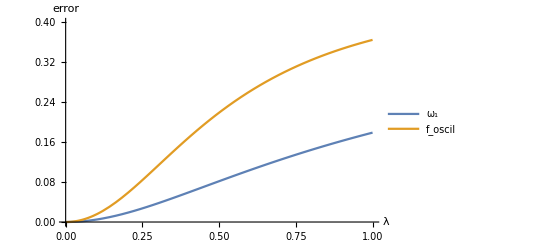

```mathematica
Plot[{ωerror[λ],oscilerror[λ]},{λ,0,1},PlotRange->{0,0.4},AxesLabel->{"λ","error"},PlotLegends->{"ω_1","f_oscil"}]
```

Taylor series of the exact transition frequency around λ and it doesn’t look converged

```mathematica
Table[D[√(3/2+λ+λ^2-1/2 √(1+4 λ^2 (2+λ+λ^2))),{λ,d}]/.λ->0,{d,10}]
```

{1/2,-5/4,-9/8,537/16,4545/32,-241245/64,-4761225/128,228756465/256,9042501825/512,-365072404725/1024}

Taylor series of the exact oscillator strength around λ and it doesn’t look converged

```mathematica
Table[D[oscil[λ],{λ,d}]/.λ->0.,{d,10}]
```

{-0.25,-1.125,-1.6875,109.031,384.609,-19883.3,-185960.,6.91078×10^6,1.25841×10^8,-3.71552×10^9}

#### Problem #11)

```mathematica
fhxc[λ_]:=λ+(λ^2 x^2)/(x^2-2-λ-λ^2)
```

```mathematica
D[fhxc[λ],{λ,1}]/.λ->0
```

1

```mathematica
D[fhxc[λ],{λ,2}]/.λ->0
```

(2 x^2)/(-2+x^2)

```mathematica
D[fhxc[λ],{λ,3}]/.λ->0
```

(6 x^2)/((-2+x^2)^2)

```mathematica
D[fhxc[λ],{λ,4}]/.λ->0
```

12 x^2 (2/((-2+x^2)^3)+2/((-2+x^2)^2))

```mathematica
D[fhxc[λ],{λ,5}]/.λ->0
```

20 x^2 (6/((-2+x^2)^4)+12/((-2+x^2)^3))

```mathematica
D[fhxc[λ],{λ,6}]/.λ->0
```

30 x^2 (24/((-2+x^2)^5)+72/((-2+x^2)^4)+24/((-2+x^2)^3))